# DG Package

```mathematica
(* Aborting after first error - Put the following two lines at the top of every notebook. *)
(* messageHandler=If[Last[#],Abort[]]&;
Internal`AddHandler["Message",messageHandler]; *)
```

## 1) Instance Creation, Plot Routines

Instance Creation: DG
DGAllEdges, DGEdgeWeight, DGEdgeDistanceBounds, DGProblem, DGSaveProblem, DGGraphGetIJD

## Source Code

```mathematica
ClearAll[
DGAllEdges,
DGEdgeWeight,
DGEdgeDistanceBounds,
DGProblem,
DGPrintGraph,
DGPrintX,
DGSaveProblem,
DGGraphGetIJD
  ];

DGAllEdges[n_] := Module[{i, j, k = 0, pij},
   pij = Table[0, {i, (n (n - 1))/2}];
   For[i = 1, i <= n, i++,
    For[j = (i + 1), j <= n, j++,
      k++;
      pij[[k]] = i <-> j;
      ];
    ];
   Return[pij]
   ];

DGEdgeWeight[G_, E_] :=
  (* Gets edge weight. 'E' can be a single edge or a list of edges; *)
  Module[
{i, eij,wij, D = {}},
If[Not[FailureQ[PropertyValue[{G, E[[1]]}, EdgeWeight]]],
(* E is a list of edges *)
For[i = 1, i <= Length[E], i++,
eij = E[[i]];
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[wij=PropertyValue[{G, eij}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]];
AppendTo[D, wij]],
(* E is a single edge *)
eij = E;
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[D = PropertyValue[{G, E}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]]
];
Return[D]
];

DGEdgeDistanceBounds[G_, E_] := Module[
   {eij = E, Lij, Uij, Vij},
   If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
   Vij = PropertyValue[{G, eij}, "DistanceBounds"];
   Return[Vij]
   ];

DGProblem[x_, eij_: {}, dijEps_: {}] :=
  (* Creates a problem P such that P["G"] is the problem graph and P["X"] is a problem solution; *)
  Module[{i, j, d, dij, k, numberOfAtoms, G, E, DijEps},
   (* set default values *)
   If[Length[eij] > 0, E = eij, E = DGAllEdges[Length[x]]];
   If[Length[dijEps] > 0, DijEps = dijEps, DijEps = Table[0, {i, Length[E]}]];
   (* unpacks the edges and calculate distances *)
   i = Table[E[[k]][[1]], {k, Length[E]}];
   j = Table[E[[k]][[2]], {k, Length[E]}];
   d = Table[N[Norm[x[[i[[k]]]] - x[[j[[k]]]]]], {k, Length[E]}];
   numberOfAtoms = Max[i, j];
   (* creates distance matrix *)
   G = Table[Infinity, {i, 1, numberOfAtoms}, {j, 1, numberOfAtoms}];
   For[k = 1, k <= Length[i], k++,
      G[[i[[k]]]][[j[[k]]]] = d[[k]];
      G[[j[[k]]]][[i[[k]]]] = d[[k]]
    ];
   (* creates the graph *)
   G = WeightedAdjacencyGraph[G];
   (* adds distance bounds *)
   If[Length[DijEps] != Length[i], Throw["InvalidInput: eij and dijEps must have the same size"]]; 
   For[k = 1, k <= Length[i], k++,
    dij = DGEdgeWeight[G, i[[k]] <-> j[[k]]];
    PropertyValue[{G, i[[k]] <-> j[[k]]}, "DistanceBounds"] = {(1 - DijEps[[k]]), (1 + DijEps[[k]])}*dij
    ];
   Return[<|"X" -> x, "G" -> G|>]
   ];

DGPrintGraph[G_]:=Module[{edges,table,eij,i,j,k,Lij,Uij,Dij},
edges=EdgeList[G];
table=Table[0,{i,Length[edges]},{j,5}];
For[k=1,k≤Length[edges],k++,
eij=edges[[k]];
{i,j}={eij[[1]],eij[[2]]};
{Lij,Uij}=DGEdgeDistanceBounds[G,eij];
Dij=DGEdgeWeight[G,eij];
table[[k]]={i,j,Dij,Lij,Uij}
];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[edges]}],{"i","j","dij","lij","uij"}}]]
];

DGPrintX[X_]:=TableForm[X, TableHeadings -> {Table[i, {i, Length[X]}], {"x", "y", "z"}}]; 

DGPrintDistanceMatrix[X_,edges_]:=Module[{E=edges,table,i,j,k},
table=Table[{i=E[[k]][[1]],j=E[[k]][[2]],N[Norm[X[[i]]-X[[j]]]]},{k,Length[E]}];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[E]}], {"i","j","dij"}}]]
];
DGPrintDistanceMatrix[X_]:=Module[{edges},
edges=DGAllEdges[Length[X]];
DGPrintDistanceMatrix[X,edges]
];

DGSaveProblem[P_, fname_] :=
  (* Create the files fname.csv and fname_xsol.csv with, respectively, the DG constraints given by P["G"] and one associated solution P["X"] *)
  Module[{edges, fid, table, eij, i, j, k, X, G, Dij, Lij, Uij},
   (* creates and saves solution table *)
   table = Table[P["X"][[i]][[j]], {i, Length[P["X"]]}, {j, 3}];
   fid = StringJoin[fname, "_xsol.csv"];
   Print["Saving solution file ", fid];
   Export[fid, table, TableHeadings -> {"x", "y", "z"}];
   (* creates and saves constraints table *)
   G = P["G"];
   edges = EdgeList[G];
   table = Table[0, {i, Length[edges]}, {j, 5}];
   For[k = 1, k <= Length[edges], k++,
    eij = edges[[k]];
    {i, j} = {eij[[1]], eij[[2]]};
    {Lij, Uij} = DGEdgeDistanceBounds[G, eij];
    Dij = DGEdgeWeight[G, eij];
    table[[k]] = {i, j, N[Dij], N[Lij], N[Uij]}
    ];
   fid = StringJoin[fname, ".csv"];
   Print["Saving constraints file ", fid];
   Export[fid, table, TableHeadings -> {"I", "J", "D", "L", "U"}];
   ];

DGGraphGetIJD[G_]:=Module[{i,j,k,d,E},
E=EdgeList[G];
i=Table[E[[k]][[1]],{k,Length[E]}];
j=Table[E[[k]][[2]],{k,Length[E]}];
d=Table[DGEdgeWeight[G,E[[k]]],{k,Length[E]}];
Return[{i,j,d}];
]
```

## Example:

```mathematica
(* DGAllEdges *)
DGAllEdges[4]
```

```mathematica
(* Creates a DGProblem with complete graph *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGPrintGraph[P["G"]]
DGPrintDistanceMatrix[x]
```

```mathematica
(* Creates a DGProblem with specific edges *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
eij = {1 <-> 2, 2 <-> 3, 3 <-> 4, 4 <-> 5};
P = DGProblem[x, eij]; 
DGPrintGraph[P["G"]]
```

```mathematica
(* Creates a DGProblem with inexact distances *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
eij = {1 <-> 2, 2 <-> 3, 3 <-> 4, 4 <-> 5};
dijEps = {0, 0.1, 0, 0.2};
P = DGProblem[x, eij, dijEps];
DGPrintGraph[P["G"]]
```

```mathematica
(* Creates a DDGroblem with limited edge size *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x, {}, {}, N[Sqrt[2]]];
DGPrintGraph[P["G"]]
```

```mathematica
(* Saves a DGProblem *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGSaveProblem[P, "c:\\Users\\Michael\\gitrepos\\github\\bioinfo\\dg_problem_small"]
```

Instance Creation: MDGP
DGSetXByCartesianSystem, DGSetXByHomogeneousCoords, DGRandom3DBackbone, DGRandomMDGP, DGCalculateProteinAngles, DGCalculateProteinAnglesForAtomAtPosition, DGCalculateTorsionAngles

## Source Code

```mathematica
ClearAll[
DGSetXByCartesianSystem,
DGSetXByHomogeneousCoords,
DGRandom3DBackbone,
DGRandomMDGP,
DGPlaneAndTorsionAngles
];
DGSetXByCartesianSystem[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using rotations and translations explicitly;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]) 
*)
Module[
(* declare local variables *)
{a,b,c,i,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[θ[[3]]],d[[3]]Sin[θ[[3]]] ,0}};
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[θ[[i]],n]; (* rotation creation *)
v=R[v]; (* rotation apply *)
(* apply torsion rotation and translation *)
R=RotationTransform[ω[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[i]]=v
];
Return[X]
];

DGSetXByHomogeneousCoords[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using transformation matrices;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]); 
*)
Module[
{B,B1,B2,B3,X,i,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
{ct,st}={Cos[θ[[3]]],Sin[θ[[3]]]};
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]ct,d[[3]]st ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[θ[[i]]],Sin[θ[[i]]]};
{cw,sw}={Cos[ω[[i]]],Sin[ω[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[i]]=v[[{1,2,3}]];
];
Return[X]
];

DGRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords",seed_:0]:=
(* Generates a random backbone in tridimensional Euclidean space;
   Input parameters;
   numberOfAtoms: number of 3D Euclidean points to be generated;
   algorithm: algorithm to be applied during coordinates calculation. The options 'are HomogeneousCoords' or 'CartesianSystem';
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on the current time is constructed;
 *)
Module[
(* declare the local variables *)
{d,θ,ω,X,output,ϵ=0.05},
(* set seed *)
If[seed>0,SeedRandom[seed]];
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
θ=Table[1.91,{i,numberOfAtoms}];
θ[[{1,2}]]={0,0};
(* torsion angles *)
ω=Table[RandomChoice[{60Degree,180Degree,300Degree}]*(1+RandomReal[{-ϵ,ϵ}]),{i,numberOfAtoms}];
ω[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=DGSetXByHomogeneousCoords[d,θ,ω],
"CartesianSystem",X=DGSetXByCartesianSystem[d,θ,ω],
_,Throw["InvalidAlgorithm:",OptionValue[algorithm]]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->ω,"CovalentBondLengths"->d,"PlaneRotationAngles"->θ|>
];

DGRandomMDGP[numberOfAtoms_,dijEps_:0.0,dijMax_:Infinity,seed_:0]:=
(* Generates a random MDGP instance.; 
   numberOfAtoms: number of 3D Euclidean points to be generated;
   dijEps: the upper (uij) and lower (lij) constraints boundaries are generated using the formulae lij = (1-dijEps) and uij = (1+dijEps); 
   dijMax: all distances greater than dijMax are dropped;
   algorithm: defines the method (algorithm) used to calculate the pairwise distances. The options are "DistanceMatrix" and "Nearest";
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on current is constructed;
*)
Module[
(* declare local variables *)
{i,j,X,D,E,dij,DijEps},
X=DGRandom3DBackbone[numberOfAtoms,"HomogeneousCoords",seed]["Points"];
E={};
DijEps={};
(* set distance bounds *)
For[i=1,i≤numberOfAtoms,i++,
For[j=i+1,j≤numberOfAtoms,j++,
(* exact distances *)
If[Abs[i-j]≤3,
AppendTo[E,{i,j}];
AppendTo[DijEps,0],
If[N[Norm[X[[i]]-X[[j]]]]<dijMax,
AppendTo[E,{i,j}];
AppendTo[DijEps,dijEps]
];
];
];
];
Return[DGProblem[X,E,DijEps]]
];

DGPlaneAndTorsionAngles[A_,B_,C_,D_,verbose_:False]:=
(* Calculates the plane and torsion for 3D points A, B, C and D in that order. *)
Module[
{nabc, nbcd,θ,ω},
(* centered at C *)
θ=VectorAngle[B-C,D-C];
If[verbose,Print["(θ):Angle[BCD]  =",θ]];
(* centered at B and C *)
{nabc,nbcd} = {Cross[A-B,C-B],Cross[B-C,D-C]};
ω=VectorAngle[nabc,nbcd];
If[verbose,Print["(ω):Angle[ABCD] =",ω]];
Return[{θ,ω}];
];

DGPlaneAndTorsionAngles[X_,i_]:=
(* Calculates plane and torsion angles of i-th atom. *)
DGPlaneAndTorsionAngles[X[[i-3]],X[[i-2]],X[[i-1]],X[[i]]];

DGPlaneAndTorsionAngles[X_]:=Module[
{θ,ω,i},
ω=Table[0,{i,Length[X]}];
θ=Table[0,{i,Length[X]}];
For[i=4,i≤Length[X],i++,
{θ[[i]],ω[[i]]}=DGPlaneAndTorsionAngles[X,i]
];
Return[{θ,ω}]
];
```

## Examples

```mathematica
(* Calculates plane and torsion angles *)
x={{0,0,1},{0,0,0},{0,1,0},{1,1,1},{0,1,1}};
{θ,ω}=DGPlaneAndTorsionAngles[x[[1]],x[[2]],x[[3]],x[[4]]]
```

```mathematica
x={{0,0,1},{0,0,0},{0,1,0},{1,1,1},{0,1,1}};
{θ,ω}=DGPlaneAndTorsionAngles[x,4]
```

```mathematica
x={{0,0,1},{0,0,0},{0,1,0},{1,1,1},{0,1,1}};
{θ,ω}=DGPlaneAndTorsionAngles[x]
```

```mathematica
(* Creates a random backbone *)
x=DGRandom3DBackbone[5,"HomogeneousCoords",0]
```

```mathematica
(* Creates a MDGP random instance with exact distances *)
P=DGRandomMDGP[5];
DGPrintGraph[P["G"]]
```

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.02707 | 3.02707 | 3.02707
4 | 1 | 5 | 3.82906 | 3.82906 | 3.82906
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 3.01344 | 3.01344 | 3.01344
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 4 | 5 | 1.526 | 1.526 | 1.526

```mathematica
(* Creates a MDGP random instance with inexact distances *)
P=DGRandomMDGP[5,0.1,4.0];
Norm[P["X"][[1]]-P["X"][[5]]]
DGPrintGraph[P["G"]]
```

4.35826

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.91614 | 2.91614 | 2.91614
4 | 2 | 3 | 1.526 | 1.526 | 1.526
5 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
6 | 2 | 5 | 3.83521 | 3.83521 | 3.83521
7 | 3 | 4 | 1.526 | 1.526 | 1.526
8 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
9 | 4 | 5 | 1.526 | 1.526 | 1.526

Plot Routines
DGPlot3DBackbone, DGPlotAdjacencyMatrix

## Source Code

```mathematica
ClearAll[
DGPlot3DBackbone,
DGPlotAdjacencyMatrix
]

DGPlot3DBackbone[X_]:=
(* Plots the points using the coordinates of X["Points"] property *)
Graphics3D[{{Red,Tube[X]},{PointSize[Large],Blue,Point[Rest[X]]},{PointSize[Large],Green,Point[First[X]]}}, Axes->True]

DGPlotAdjacencyMatrix[G_,DiagonalCovering_:False]:=Module[
{i,j,n,ei,ej,edges,primitives,add},
n=Max[VertexList[G]];
edges=EdgeList[G];
(* inverting edges position *)
edges=Table[{edges[[i]][[2]],n-edges[[i]][[1]]+1},{i,Length[edges]}];
primitives={
{PointSize[Medium],Point[edges]},
{Red,Dashed,Line[{{1,n},{n,1}}]}
};
(* Plot diagonal covering *)
If[DiagonalCovering,
For[i=1,i≤Length[edges],i++,
add=True;
ei=edges[[i]];
For[j=1,j≤Length[edges],j++,
ej=edges[[j]];
If[(ej[[1]]==ei[[1]]&&ej[[2]]>ei[[2]]),add=False];
If[(ej[[2]]==ei[[2]]&&ej[[1]]>ei[[1]]),add=False];
];
If[add,
PrependTo[primitives,
{Opacity[0.2],Red,Triangle[{{ei[[1]],n+1-ei[[1]]},ei,{n+1-ei[[2]],ei[[2]]}}]}]
];
];
];
Graphics[primitives,
Axes->True,
GridLines->Automatic,
Ticks->{Automatic,Table[{i,n+1-i},{i,n}]},
AxesOrigin->{1,1}
]
];
```

## Examples

```mathematica
(* Plot a simple a backbone *)
x=DGRandom3DBackbone[5];
DGPlot3DBackbone[x["Points"]]
```

```mathematica
(* Plot adjacency matrix *)
P=DGRandomMDGP[10];
DGPlotAdjacencyMatrix[P["G"],True]
```

## 2) Check Solution and Standard Solvers

Solution Analysis
DGRelativeError, DGLDME, DGRMSD

## Source Code

```mathematica
ClearAll[DGRelativeError,DGRMSD,DGLDME]
DGRelativeError[G_,X_,verbose_:False]:=Module[
{i,j,k,lij,uij, dij,numberOfEdges,E,error},
E=EdgeList[P["G"]];
numberOfEdges=Length[E];
error=Table[0,{i,numberOfEdges}];
For[k=1,k≤numberOfEdges,k++,
{i=E[[k]][[1]],j=E[[k]][[2]]};
{lij,uij}=DGEdgeDistanceBounds[G,i<->j];
dij=Norm[X[[i]]-X[[j]]];
error[[k]]=Max[Max[{0,lij-dij}]/lij,Max[{0,dij-uij}]/uij];
];
If[verbose,
Print["Solution Quality"];
Print["Number of nodes      : ",Length[X]];
Print["Number of edges      : ",Length[E]];
Print["Relative error bounds: ",{Min[error],Max[error]}];
Print["Mean relative error  : ",Mean[error]]];
Return[error]
];

DGRelativeError[G_,X_,i_,nodes_]:=
(* Calculates the relative error of the nodes[[i]] considering only the nodes[[1;;i-1]] *)
Module[
(* local variables *)
{eij,j,k,V,Xi,Xj,Dij,Lij,Uij,errorDij,nid},
(* current position *)
Xi=X[[nodes[[i]]]];
(* indentifies which nodes has been already fixed *)
nid=Table[0,{k,i}];
For[k=1,k≤i,k++,
nid[[nodes[[k]]]]=k
];
(* considering only the precedent nodes *)
V= Select[AdjacencyList[G,nodes[[i]]],MemberQ[nid,#]&];
(*Print["V=",V];*)
errorDij=0.0;
For[k=1,k≤Length[V],k++,
(* neighbor index *)
j=V[[k]];
(* neighbor coordinate *)
Xj=X[[j]];
(* actual distance *)
Dij=EuclideanDistance[Xi,Xj];
(* distance bounds *)
{Lij,Uij}=DGEdgeDistanceBounds[G,i<->j];
(* error Dij *)
eij=Max[(Lij-Dij)/Lij,(Dij-Uij)/Uij];
(* update error *)
If[eij>errorDij,errorDij=eij];
];
Return[errorDij]
];

DGLDME[G_,X_]:=Module[
{i,j,k,E,ldme=0,lij,uij,dij},
E=EdgeList[G];
For[k=1,k≤Length[E],k++,
{lij,uij}=DGEdgeDistanceBounds[G,E[[k]]];
i=E[[k]][[1]];
j=E[[k]][[2]];
dij=Norm[X[[i]]-X[[j]],2];
ldme+=Max[lij-dij,dij-uij,0]^2
];
Return[Sqrt[ldme/Length[E]]]
];

DGRMSD[X_,Y_]:=Module[
{xc,yc,x,y,U,D,V,rmsd},
(* calculating centers *)
xc=Mean[X];
yc=Mean[Y];
(* translation *)
x=Table[X[[i]]-xc,{i,Length[X]}];
y=Table[Y[[i]]-yc,{i,Length[Y]}];
(* svd *)
V=Transpose[x].y;
{U,D,V}=SingularValueDecomposition[V];
V=U.Transpose[V];
x=x.V;
rmsd=Norm[x-y,"Frobenius"]/Sqrt[Length[x]];
Return[{rmsd,V,x,y}]
]
```

## Examples

```mathematica
(* DGRMSD *)
X={{0.814700,0.097500,0.157600},{0.905800,0.278500,0.970600},{0.127000,0.546900,0.957200},{0.913400,0.957500,0.485400},{0.632400,0.964900,0.800300}};
Y={{6.167723,5.509229,5.376972},{5.921716,5.625914,6.161379},{5.265461,5.705450,6.339958},{5.936486,6.432611,5.883000},{5.680966,5.982123,5.893736}};
{MatrixForm[X],MatrixForm[Y]}
{rmsd,Q,x,y}=DGRMSD[X,Y];
{rmsd,MatrixForm[Q],MatrixForm[x],MatrixForm[y]}
```

```mathematica
(* Check relative error *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGRelativeError[P["G"],x,True]
DGRelativeError[P["G"],x+RandomReal[0.1,Length[x]],True]
```

```mathematica
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
x[[4]]+=0.1;
DGRelativeError[P["G"],x,4,{1,2,3,4,5}]
```

General Methods
DGNSolve, DGAllInstancesSolver, DGOptSolver

## DGNSolve - Nonlinear equations

### Source Code

```mathematica
ClearAll[DGNSolve]
DGNSolve[G_]:=Module[{k,i,j,d,d12,eqs,xi,xj,x,n},
{i,j,d}=DGGraphGetIJD[G];
eqs=Table[0,{k,Length[i]}];
n=Max[i,j];
x=Table[Symbol[StringJoin["x",ToString[xi],ToString[xj]]],{xi,n},{xj,3}];
For[k=1,k≤Length[i],k++,
xi=x[[i[[k]]]];
xj=x[[j[[k]]]];
eqs[[k]]=(xi[[1]]-xj[[1]])^2+(xi[[2]]-xj[[2]])^2+(xi[[3]]-xj[[3]])^2==d[[k]]^2
];
(* set some points *)
d12=DGEdgeWeight[G,1<->2];
eqs=Join[eqs,
{x[[1]][[1]]==0,x[[1]][[2]]==0,x[[1]][[3]]==0,
x[[2]][[1]]==d12,x[[2]][[2]]==0,x[[2]][[3]]==0}
];
Print["eqs=",TableForm[eqs]];
x=Flatten[x];
Quiet[x=NSolve[eqs,x,Reals]];
x=ArrayReshape[x,{n,3}];
Print["x=",TableForm[x]];
(* convert relations to scalar matrix *)
If[Length[x[[1]][[1]]]>1,x=Table[x[[i]][[j]][[2]],{i,n},{j,3}]];
Return[x]
];
```

### Examples

#### Example: 5 points and 4 constraints

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
TableForm[x,TableHeadings->{Table[i,{i,Length[x]}],{"x","y","z"}}]
DGRelativeError[P["G"],x,True];
```

#### Example: 5 points and 4 constraints (failed)

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
DGRelativeError[P["G"],x,True];
```

#### Example: 5 points and all constraints

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
TableForm[x,TableHeadings->{Table[i,{i,Length[x]}],{"x","y","z"}}]
DGRelativeError[P["G"],x,True];
```

#### Example: 5 points and all constraints (failed)

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
DGRelativeError[P["G"],x,True];
```

## DGOptSolver - Optimization

### Source Code

```mathematica
ClearAll[DGOptSolverFobj,DGOptSolver]
```

```mathematica
DGOptSolverFobj[i_,j_,d_,x_]:=Module[{f=0,numberOfAtoms,ncols,nrows,k,y},
y=ArrayReshape[x,{Length[x]/3,3}];
For[k=1,k≤Length[d],k++,
f+=(d[[k]]^2-Norm[y[[i[[k]]]]-y[[j[[k]]]]]^2)^2
];
Return[f]
]
DGOptSolver[G_]:=Module[{numberOfAtoms,f,y,v,w,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
ClearAll[z];
y=Array[z,3*numberOfAtoms];
f:=DGOptSolverFobj[i,j,d,#]&;
{v,y}=NMinimize[f[y],y];
y=ArrayReshape[y,{Length[y]/3,3}];
y=Table[y[[iloc]][[jloc]][[2]],{iloc,Length[y]},{jloc,3}];
Return[y]
]
```

### Examples

```mathematica
(* Example C: Solving an instance with 5 points using optimization based method *)
x=RandomReal[1,{5,3}];
eij={{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{4,5}};
P=DGProblem[x,eij];
y=DGOptSolver[P["G"]];
DGRelativeError[P["G"],y,True];
```

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGOptSolver[P["G"]];
DGRelativeError[P["G"],x,True];
```

```mathematica
(* Example D: Solving an instance with 100 points using optimization based method *)
(* It can take a lot of time!!! *) 
(* For[k=1,k≤100,k++,
SeedRandom[k];
x=RandomReal[1,{7,3}];
eij=MDGAllPairs[Length[x]];
eij=RandomSample[eij,Round[0.50Length[eij]]];
{i,j,d}=MDGCreateInstanceFromSolutionAndPairs[x,eij];
y=MDGOptSolver[i,j,d];
f=CheckMDGSolution[i,j,d,y,False];
If[Or[f>0.01,Mod[k,10]==0],
Print["{Seed,Error}=",{k,f}];
];
]
*)
```

## DGAllIstancesSolver - Solver for complete distance matrices

### Source Code

```mathematica
ClearAll[DGAllInstancesSolver]
DGAllInstancesSolver[G_]:=Module[{numberOfAtoms,k,m,λ,v,x,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
(* creates distance matrix *)
m=Table[0,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
For[k=1,k≤Length[i],k++,
m[[i[[k]]]][[j[[k]]]]=d[[k]];
m[[j[[k]]]][[i[[k]]]]=d[[k]];
];
(* λ:eigenvalues and v:eigenvectors *)
m=Table[(m[[1]][[iloc]]^2+m[[1]][[jloc]]^2-m[[iloc]][[jloc]]^2)/2,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
{λ,v}=Eigensystem[m,3];
(* getting solution *)
x=Table[Sqrt[λ[[jloc]]]v[[jloc]][[iloc]],{iloc,numberOfAtoms},{jloc,3}];
Return[x]
]
```

### Examples

#### Example: 5 points and 4 constraints where DGNSolve fails

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGAllInstancesSolver[P["G"]];
DGRelativeError[P["G"],x,True];
```

#### Example: 100 points all constraints

```mathematica
x=RandomReal[1,{100,3}];
P=DGProblem[x];
x=DGAllInstancesSolver[P["G"]];
DGRelativeError[P["G"],x,True];
```

## 3) Ordering, BuildUP and BP

Ordering
DGOrdering

### Source Code

```mathematica
ClearAll[DGOrdering]
DGOrdering[G_,C_,verbose_:False]:=
(* Finds an order such that all atoms could be determined by following it; 
   C: Initial clique used to start the ordering;
   G: Instance graph;
*)
Module[{i,j,k,neighs,nAtoms,nFixedAtoms,nFixedNeighs,atomsToBeFixed,atomOrder, order,minNeighsToBeFixed},
(* initial values *)
minNeighsToBeFixed=Length[C];
nAtoms=Length[VertexList[G]];
nFixedNeighs=Table[0,{i,nAtoms}];
atomOrder=Table[0,{i,nAtoms}];
atomsToBeFixed=C;
nFixedNeighs[[C]]=Infinity;
nFixedAtoms=0;
While[Length[atomsToBeFixed]>0,
If[verbose,
Print["nFixedNeighs=",nFixedNeighs];
Print["atomsToBeFixed=",atomsToBeFixed];
];
i=First[atomsToBeFixed];
(* remove the first element *)
atomsToBeFixed=Rest[atomsToBeFixed];
(* skipped: already fixed *)
If[atomOrder[[i]]>0,Continue[]];
If[verbose,Print["Fixing: ",i]];
atomOrder[[i]]=++nFixedAtoms;
If[verbose,Print["atomOrder=",atomOrder]];
(* update neighs score *)
neighs=AdjacencyList[G,i];
If[verbose,Print["neighs=",neighs]];
For[k=1,k≤Length[neighs],k++,
j=neighs[[k]];
nFixedNeighs[[j]]++;
If[atomOrder[[j]]==0&&nFixedNeighs[[j]]≥minNeighsToBeFixed &&Not[MemberQ[atomsToBeFixed,j]],
AppendTo[atomsToBeFixed,j];
];
]
];
If[nFixedAtoms≠nAtoms,Throw["InvalidOrdering: It has not been possible the set ordering."]];
order=Table[i,{i,nAtoms}];
order[[atomOrder]]=order;
Return[order];
]
```

### Examples

#### Simple Example: The initial ordering is ok!

```mathematica
G=Graph[{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}];
{GraphPlot[G,VertexLabeling->True],DGPlotAdjacencyMatrix[G,True]}
i=DGOrdering[G,{1,2,3,4},True]
```

#### Harder Example: The initial ordering is not valid

```mathematica
edges={1<->2,1<->3,1<->4,1<->7,1<->8,2<->3,2<->4,2<->5,2<->6,2<->8,3<->4,3<->7,3<->8,4<->6,4<->7,4<->8,4<->5,5<->6,5<->7,6<->7,6<->8,7<->8};
G=Graph[edges];
{GraphPlot[G,VertexLabeling->True],DGPlotAdjacencyMatrix[G,True]}
i=DGOrdering[G,{1,2,3,4},True]
```

Intersection of spheres
DGIntersect3Spheres, DGIntersect4Spheres

```mathematica
ClearAll[DGIntersect3Spheres,DGIntersect4Spheres];
DGIntersect3Spheres[a_,ra_,b_,rb_,c_,rc_]:=
(* Gets the 2 solutions of {||x-a||=ra,||x-b||=rb,||x-c||=rc};
   Input;
   a,b,c: sphere centers;
   ra,rb,rc: respective sphere radius;
   Output;   
   x: the two intersections (x[[1]]: positive chirality and x[[2]]: negative chirality);
 *)
Module[{n,A,x,p,dp,u,v,w,du,dv,dw,dpu,AbsCos,error},
(* select the most perpendicular vertex angle (stability) *)
AbsCos[u_,v_]:=Dot[u,v]/(Norm[u]*Norm[v]);
{u,v,w,du,dv,dw}=MinimalBy[{
{AbsCos[b-a,c-a],{a,b,c,ra,rb,rc}},
{AbsCos[c-b,a-b],{b,c,a,rb,rc,ra}},
{AbsCos[a-c,b-c],{c,a,b,rc,ra,rb}}
},First][[1]][[2]];
(* normal to the plane (u,v,w) *)
n=Normalize[Cross[v-u,w-u]];
A={v-u,w-u,n};
x={(Dot[v,v]-Dot[u,u]-dv^2+du^2)/2,(Dot[w,w]-Dot[u,u]-dw^2+du^2)/2,Dot[n,u]};
p=LinearSolve[A,x];
(* select the factor with minimal canceling effect (stability) *)
{u,du}=MaximalBy[{
{Abs[(ra-Norm[p-a])/ra],{a,ra}},
{Abs[(rb-Norm[p-b])/rb],{b,rb}},
{Abs[(rc-Norm[p-c])/rc],{c,rc}}
},First][[1]][[2]];
dpu=Norm[p-u];
dp=N[Sqrt[(du+dpu)*(du-dpu)]];
dp=Re[dp];
x={p+dp*n,p-dp*n};
(* calculating max relative errors of each solution *)
error=Table[Max[Abs[{(Norm[a-x[[i]]]-ra)/ra,(Norm[b-x[[i]]]-rb)/rb,(Norm[c-x[[i]]]-rc)/rc}]],{i,2}];
Return[{x,error}];
];

DGIntersect4Spheres[a_,ra_,b_,rb_,c_,rc_,d_,rd_]:=
Module[{x,error},
{x,error}=DGIntersect3Spheres[a,ra,b,rb,c,rc];
If[Abs[Norm[x[[1]]-d]-rd]<Abs[Norm[x[[2]]-d]-rd],
x=x[[1]];
error=error[[1]],
x=x[[2]];
error=error[[2]]];
Return[{x,error}]
];
```

BuildUpSolver

### Source Code

```mathematica
ClearAll[
DGBuildUpInitX,
DGBuildUpSetX,
DGBuildUpSolver
]

DGBuildUpInitX[G_,basis_]:=Module[
{i1,i2,i3,i4,d12,d13,d14,d23,d24,d34,A,X21,X31,X32,X41,X42,error},
{i1,i2,i3,i4}=basis;
d12=DGEdgeWeight[G,i1<->i2];
d13=DGEdgeWeight[G,i1<->i3];
d14=DGEdgeWeight[G,i1<->i4];
d23=DGEdgeWeight[G,i2<->i3];
d24=DGEdgeWeight[G,i2<->i4];
d34=DGEdgeWeight[G,i3<->i4];
(* set the position of the four atoms in the basis *)
X=Table[{0,0,0},{i,Length[VertexList[G]]}];
X[[i2]][[1]]=d12;
X21=X[[i2]][[1]];
X[[i3]][[1]]=(d13^2-d23^2+X21^2)/(2*X21);
X31=X[[i3]][[1]];
X[[i3]][[2]]=Sqrt[d13^2-X31^2];
{X[[i4]],error}=DGIntersect3Spheres[X[[i1]],d14,X[[i2]],d24,X[[i3]],d34][[1]];
Return[X];
];

DGBuildUpSetX[G_,X_,nodes_,i_]:=Module[
{j,k,neighs,basis,x,i1,i2,i3,i4,d1,d2,d3,d4,error},
k=nodes[[i]];
neighs=Intersection[AdjacencyList[G,k],nodes[[1;;(i-1)]]];
If[Length[neighs]<4,Throw["InvalidOrder: There is not enough neighs to set a basis"]];
basis=Subsets[neighs,{4}];
For[j=1,j≤Length[basis],j++,
{i1,i2,i3,i4}=basis[[j]];
d1=DGEdgeWeight[G,i1<->k];
d2=DGEdgeWeight[G,i2<->k];
d3=DGEdgeWeight[G,i3<->k];
d4=DGEdgeWeight[G,i4<->k];
{x,error}=DGIntersect4Spheres[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3,X[[i4]],d4];
If[error<10^(-3),Break];
];
Return[x]
];

DGBuildUpSolver[G_,nodes_]:=Module[
{i,X},
X=DGBuildUpInitX[G,nodes[[1;;4]]];
(* set remaining atoms *)
For[i=5,i≤Length[X],i++,
X[[nodes[[i]]]]=DGBuildUpSetX[G,X,nodes,i]
];
Return[X]
];
```

### Example

#### Check DGBuildUpInitX

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
edges={{1,2},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}};
P=DGProblem[x,edges];
DGPrintGraph[P["G"]]
basis={2,3,4,5};
x=DGBuildUpInitX[P["G"],basis];
DGPrintDistanceMatrix[x,edges]
```

#### Check DGBuildUpSolver

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
edges={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}};
P=DGProblem[x,edges];
nodes={1,2,3,5,4};
x=DGBuildUpSolver[P["G"],nodes];
DGPrintX[x]
DGRelativeError[P["G"],x,True];
```

#### Solving an instance using BuilUpSolver method

```mathematica
P=DGRandomMDGP[20,0.0,5.0,0];
X=P["X"];
G=P["G"];
nodes=Table[i,{i,Length[VertexList[G]]}]
X=DGBuildUpSolver[G,nodes];
DGRelativeError[G,X,True];
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Solution Quality

Number of nodes      : 20

Number of edges      : 135

Relative error bounds: {0.,3.11386×10^-14}

Mean relative error  : 2.92878×10^-15

## Solving Manually: Continuos Problem

```mathematica
GetEuclideanCoords[θ_]:=Module[{n,d=1.526,ϕ=1.91,a,b,c,i,p,u,v,x},
n=Length[θ];
x=Table[0,{i,n},{j,3}];
x[[{1,2,3}]]={{0,0,0},{-d,0,0},{-d+d*Cos[ϕ],d*Sin[ϕ] ,0}};
For[i=4,i≤n,i++,
(* dihedral rotation axis *)
{a,b,c}={x[[i-3]],x[[i-2]],x[[i-1]]};
u=Normalize[b-c];
p= c+d* u; 
(* normal to the plane abc *)
v=Cross[b-c,a-c];
(* plane rotation *)
p=RotationTransform[ϕ,v,c][p];
(* dihedral rotation *)
p=RotationTransform[θ[[i]],u,c][p];
(* set i-th coordinate *)
x[[i]]=p
];
Return[x]
];
```

```mathematica
MDGErrorMatrix[i_,j_,d_,X_]:=Module[{k,ei,ej,M},
M=Table[0,{xi,Length[x]},{xj,Length[x]}];
For[k=1,k≤Length[i],k++,
ei=i[[k]];
ej=j[[k]];
M[[ei]][[ej]]=Norm[X[[ei]]-X[[ej]]]-d[[k]];
M[[ej]][[ei]]=M[[ei]][[ej]];
];
Return[M]
];
```

```mathematica
ω={0,0,0,RandomReal[{-Pi,Pi}],RandomReal[{-Pi,Pi}],RandomReal[{-Pi,Pi}],RandomReal[{-Pi,Pi}],RandomReal[{-Pi,Pi}],RandomReal[{-Pi,Pi}]}
x=GetEuclideanCoords[ω];
eij=MDGAllPairs[Length[x]];
{i,j,d}=MDGCreateInstanceFromSolutionAndPairs[x,eij];
MatrixForm[MDGErrorMatrix[i,j,d,x]]
```

```mathematica
DynamicModule[{},
Manipulate[{
Graphics3D[{
{Red,Tube[GetEuclideanCoords[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]]},
{PointSize[Large],Blue,Point[GetEuclideanCoords[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]]}},
PlotRange->{xrange,yrange,zrange},
RotationAction->"Clip",
Axes->True,
AxesLabel->{"x","y","z"},
BoxStyle->Directive[Dashed],
ImageSize->Medium],
MatrixPlot[
MDGErrorMatrix[i,j,d,GetEuclideanCoords[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]],
ImageSize->Small,
ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-3,3}]]&),ColorFunctionScaling->False]},
(* Torsion angles *)
Style["Torsion Angles",Bold,Medium],
{{ω4,0},-Pi,Pi},
{{ω5,0},-Pi,Pi},
{{ω6,0},-Pi,Pi},
{{ω7,0},-Pi,Pi},
{{ω8,0},-Pi,Pi},
{{ω9,0},-Pi,Pi},
(* Bounding boxes *)
Style["Bounding Limits",Bold,Medium],
{{xrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
{{yrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
{{zrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
OpenerView[
{Style["Solution",Bold, Medium],
Column[
{Row[{"ω4  ",Slider[ω[[4]],{-Pi,Pi},Enabled->False]}],
Row[{"ω5  ",Slider[ω[[5]],{-Pi,Pi},Enabled->False]}],
Row[{"ω6  ",Slider[ω[[6]],{-Pi,Pi},Enabled->False]}],
Row[{"ω7  ",Slider[ω[[7]],{-Pi,Pi},Enabled->False]}],
Row[{"ω8  ",Slider[ω[[8]],{-Pi,Pi},Enabled->False]}],
Row[{"ω9  ",Slider[ω[[9]],{-Pi,Pi},Enabled->False]}]}]}],
ControlPlacement->Left]
]
```

## BPSolver

### Source Code

```mathematica
(* check; 
x={0,0,0};
a=RandomReal[10,3];
b=RandomReal[10,3];
c=RandomReal[10,3];
da=Norm[x-a];db=Norm[x-b];dc=Norm[x-c];
Print[TableForm[{BPGetNodePosition[a,b,c,da,db,dc,0],BPGetNodePosition[a,b,c,da,db,dc,1]}]]
*)
```

```mathematica
BPSetXinit[G_,order_:{}]:=Module[{i,j,k,numberOfAtoms,dAB,dAC,dBC,tABC,X},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{i,numberOfAtoms}];
(* three first atoms *)
If[Length[order]>0, 
{i,j,k}=Sort[order[[1;;3]]],
{i,j,k}={1,2,3}
];
{dAB,dAC,dBC}=GetEdgeWeight[G,{i<->j,i<->k,j<->k}];
(* planar rotation angle for third atom *)
tABC=ArcCos[(dAB^2+dBC^2-dAC^2)/(2*dAB*dBC)];
(* set the position of the three first points *)
X[[{i,j,k}]]={{0,0,0},{-dAB,0,0},{-dAB+dBC*Cos[tABC],dBC*Sin[tABC] ,0}};
Return[X];
]

BPGetNextCoord[G_,i_,j_,k_,branch_,node_,X_]:=Module[{di,dj,dk},
{di,dj,dk}={GetEdgeWeight[G,i<->node],GetEdgeWeight[G,j<->node],GetEdgeWeight[G,k<->node]};
Return[BPGetNodePosition[X[[i]],X[[j]],X[[k]],di,dj,dk,branch]]
];

BPGetNextBasis[G_,order_,node_]:=Module[{i,neighs,nodeOrder,basis={}},
nodeOrder=Table[0,{i,Max[order]}];
For[i=1,i≤Length[order],i++,
nodeOrder[[order[[i]]]]=i
];
neighs=AdjacencyList[G,order[node]];
For[i=1,i≤neighs,i++,
If[nodeOrder[[neighs[[i]]]]<nodeOrder[[node]],
AppendTo[basis,neighs[[i]]];
];
If[Length[basis]==3,Break];
];
If[Length[basis]<3,Throw["InvalidOrdering"]];
Return[basis];
];

BPSolver[G_,order_:{}]:=
(* Calculate all solutions of the DMDG instance defined by the graph G. *)
Module[
(* local variables *)
{di,dj,dk,i,j,k,tABC,dAB,dAC,dBC,numberOfAtoms,prune,node,branch,X,S,work,tol=10^(-5)},
numberOfAtoms=Length[VertexList[G]];
(* set default order *)
If[Length[order]==0,order=Table[i,{i,numberOfAtoms}]];
(* init atoms positions on Euclidean 3d space *)
X=BPSetXinit[G,order];
(* init BPTree *)
{branch=Table[0,{i,numberOfAtoms}],branch[[{1,2,3}]]=1};
{node=3,prune=False};
{work=Table[0,{i,numberOfAtoms}],work[[{1,2,3}]]=1};
(* BP core *)
S=<|"Points"->{},"Branches"->{}|>; (* solutions *)
While[True,
(* go to next node *)
If[prune|| node==numberOfAtoms,
(* if pruned or last node, search for a node to branch *)
i=node; prune=False;
While[i>0,If[branch[[i]]==0,branch[[i]]=1;Break[]];i--];
(* stop criterion (there is no next node) *)
If[i==0,Break[]];
(* reset lower (until k) tree levels *)
For[j=i+1,j≤node,j++,branch[[j]]=0];
node=i,
(* if not pruned nor last node, just go to the child node *)
node++
];
(* calculate position of current node *)
work[[node]]++;
{i,j,k}=BPGetNextBasis[G,node,order];
X[[order[[node]]]]=BPGetNextCoord[G,i,j,k,branch[[node]],order[[node]],X];
(* prune *)
If[CalculatePartialSolutionError[G,X,order,node]>tol,prune=True;Continue[]];
(* new solution found *)
If[node==numberOfAtoms,AppendTo[S["Points"],X];AppendTo[S["Branches"],branch]];
];
(*Print["A total of ", Length[S["Points"]]," solutions has been found."];*)
Return[{S,work}]
];

BPPlotEstimatedComplexity[G_]:=
(* Estimates a tight upper bound to the number of solutions given by the connectivity graph G *)
Module[
(* local variables *)
{numberOfAtoms,i,j,k,work,choices,V,R,reduced},
If[Not[IsNaturalOrderValid[G]],Throw["InvalidOrdering"]];
numberOfAtoms=Length[VertexList[G]];
{work=Table[1,{i,numberOfAtoms}],work[[4]]=2};
{choices=Table[Infinity,{i,numberOfAtoms}],choices[[{1,2,3,4}]]={1,1,1,2}};
For[i=5,i≤numberOfAtoms,i++,
(* only edges with precedent vertices *)
V=Select[AdjacencyList[G,i],#<i&];
work[[i]]=2*choices[[i-1]];
If[Length[V]<4,
(* there is no additional constraint *)
choices[[i]]=work[[i]],
(* take the four most restrictive constraints *)
R=Table[choices[[V[[j]]]],{j,Length[V]}];
(* minimal number of choices *)
k=RankedMin[R,4];
(* minimal index with minimal number of choices *)
k=Min[Select[V,(choices[[#]]==k)&]];
(* update intermediate number of choices *)
For[j=(k+1),j≤i,j++,If[choices[[j]]>choices[[k]],choices[[j]]=choices[[k]]]];
];
];
Print["Estimated number of Solutions ",choices[[numberOfAtoms]],"."];
ListLinePlot[work,Filling->Axis, PlotLegends->{"Estimated"}]
];
```

### Examples and Applications

#### Calculating the number of solution as a function of the number of constraints (max distance)

```mathematica
x={0,0,1};
a={0,0,0};
b={1,0,0};
c={0,1,0};
da=Norm[x-a];db=Norm[x-b];dc=Norm[x-c];
BPGetNodePosition[a,b,c,da,db,dc,0]
BPGetNodePosition[a,b,c,da,db,dc,1]
```

#### Calculating the number of solution as a function of the number of constraints (max distance)

```mathematica
(* set graph *)
G=GenerateRandomMDG[10,Infinity]["G"];
allEdges=EdgeList[G];
```

```mathematica
Needs["ErrorBarPlots`"]
nSample=25;
density={0,0.1,0.2,0.3,0.4,0.5};
nSols=Table[0,{i,Length[density]},{j,nSample}];
g=Table[0,{i,Length[density]},{j,nSample}];
For[i=1,i≤Length[density],i++,
d=density[[i]];
For[j=1,j≤nSample,j++,
(* create subgraph *)
gij=G;
For[k=1,k≤Length[allEdges],k++,
ek=allEdges[[k]];
If[RandomReal[]>d&&Abs[ek[[1]]-ek[[2]]]>3,gij=EdgeDelete[gij,ek]]
];
g[[i]][[j]]=gij;
(* solve instance *)
{S,work}=BPSolver[gij];
nSols[[i]][[j]]=Length[S["Points"]];
];
];
ErrorListPlot[Table[{{density[[i]],Mean[nSols[[i]]]},ErrorBar[StandardDeviation[nSols[[i]]]]},{i,Length[density]}],
Joined->True,
AxesLabel->{"Density of Edges", "Number of Solutions"}]
```

```mathematica
nSols[[-3]]
```

```mathematica
{MatrixPlot[UpperTriangularize[AdjacencyMatrix[g[[-3]][[1]]],3],MaxPlotPoints->Infinity],
MatrixPlot[UpperTriangularize[AdjacencyMatrix[g[[-3]][[-4]]],3]]}
```

```mathematica
M={{Circle[],0},{0,Circle[]}}
MatrixForm
```

```mathematica
{S,work}=BPSolver[G];
```

```mathematica
meanNSols=Table[Mean[nsols[[i]][[j]]],{i,Length[nAtoms]},{j,Length[maxDistance]}];
meanEdges=Table[Mean[nedges[[i]][[j]]],{i,Length[nAtoms]},{j,Length[maxDistance]}];
(* plot nsols *)
data=Table[Table[{maxDistance[[i]],meanNSols[[j]][[i]]},{i,Length[maxDistance]}],{j,Length[meanNSols]}];
ListLinePlot[data,PlotLegends->Table[StringJoin["N=", ToString[nAtoms[[j]]]],{j,Length[nAtoms]}]]
(* plot nedges *)
data=Table[Table[{maxDistance[[i]],meanEdges[[j]][[i]]},{i,Length[maxDistance]}],{j,Length[meanNSols]}];
ListLinePlot[data,PlotLabels->Table[StringJoin["N=", ToString[nAtoms[[j]]]],{j,Length[nAtoms]}]]
```

#### Solving an instance using BPSolver

```mathematica
(* easy case using natural order *)
M=GenerateRandomMDG[9,5];
G=M["G"];
{S,work}=BPSolver[M["G"]]
```

```mathematica
(* natural order does not work *)
X=RandomReal[8,3];
edges={1<->2,1<->3,1<->4,1<->7,1<->8,2<->3,2<->4,2<->5,2<->6,2<->8,3<->4,3<->7,3<->8,4<->6,4<->7,4<->8,4<->5,5<->6,5<->7,6<->7,6<->8,7<->8};
G=Graph[edges];
```

#### Estimating the number of solutions

```mathematica
Timing[M=GenerateRandomMDG[7,4];]
X=M["X"];
G=M["G"];
Timing[{S,work}=BPSolver[G];]
Show[ListPlot[work,PlotStyle->Red,PlotMarkers->{Automatic,Small},PlotLegends->{"Real"}],BPPlotEstimatedComplexity[G],AxesLabel->{HoldForm[Atom ID],HoldForm[Computed Locations]},PlotLabel->HoldForm[Computational Effort]]
CheckMDGSolutionQuality[G,S["Points"][[1]]]
(* MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"TemperatureMap"] *)
(* MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"Monochrome"] *)
```

## Solving Manually: Discrete Problem

### Source : CreateTreeGraphFromBranches

```mathematica
ClearAll[CreateTreeGraphFromBranches]
CreateTreeGraphFromBranches[G_,branch_,branches_,check_]:=Module[
{T,X,k,i,n,b,x,y,z,dx,dy,dz,edges={},v={},styVertex,styEdges={},m,color,valid},
n=Length[VertexList[G]]-3;
(* creating edges *)
For[k=1,k≤2^n-1,k++,
AppendTo[edges,k<->2k];
AppendTo[edges,k<->2k+1];
];
(* highlighting current branch *)
For[k=0,k≤n,k++,
AppendTo[v,FromDigits[Join[{1},branch[[1;;k]]],2]];
If[k>0,
AppendTo[styEdges,v[[k]]<->v[[k+1]]->{Blue,Thickness[0.01]}]
];
];
(* coloring visited nodes (branches) *)
styVertex={LightGray};
If[Length[branches]>0,
For[k=1,k≤Length[branches],k++,
X=BPSetXinit[G];
b=branches[[k]];
If[check,
(* checking partial solutions *)
valid=True;
For[i=1,i≤n,i++,
{x,y,z}={i,i+1,i+2};
X[[i+3]]=BPGetNextCoord[G,x,y,z,b[[i]],i+3,X];If[valid&&CalculatePartialSolutionError[G,X,i+3]<0.001,
color=Green,
valid =False;
color=Red;
];
v=FromDigits[Join[{1},b[[1;;i]]],2];
AppendTo[styVertex,v->color]
],
(* checking only final solution *)
valid=True;
For[i=1,i≤n,i++,
{x,y,z}={i,i+1,i+2};
X[[i+3]]=BPGetNextCoord[G,x,y,z,b[[i]],i+3,X];
If[CalculatePartialSolutionError[G,X,i+3]>0.001,
valid=False
];
If[valid,color=Green,color=Red];
v=FromDigits[Join[{1},b],2];
AppendTo[styVertex,v->color]
],
];
];
];
T=TreeGraph[
edges,
VertexStyle->styVertex,
EdgeStyle->styEdges,
GraphLayout->{"LayeredEmbedding",LayerSizeFunction->(8&)}
];
Return[T];
];
```

### Source Code : Solver

```mathematica
G=GenerateRandomMDG[9,5]["G"];
edges=EdgeList[G];
ei=Table[edges[[k]][[1]],{k,Length[edges]}];
ej=Table[edges[[k]][[2]],{k,Length[edges]}];
dij =Table[GetEdgeWeight[G,edges[[k]]],{k,Length[edges]}];
DynamicModule[{branches={},b={},s={},X=BPSetXinit[G]},
Manipulate[
Row[{CreateTreeGraphFromBranches[G,{ω4,ω5,ω6,ω7,ω8,ω9},branches,BP],
Column[
{PlotAdjacencyMatrix[G,Sym],
Graphics3D[{
{Red,Tube[X]},
{PointSize[Large],Blue,Point[X]}}],
MatrixForm[s,TableHeadings->{None,{"ω4","ω5","ω6","ω7","ω8","ω9"}}]}]}],
(* Branches *)
Style["Branches",Bold,Medium],
{ω4,{0,1},ControlType->SetterBar},
{ω5,{0,1},ControlType->SetterBar},
{ω6,{0,1},ControlType->SetterBar},
{ω7,{0,1},ControlType->SetterBar},
{ω8,{0,1},ControlType->SetterBar},
{ω9,{0,1},ControlType->SetterBar},
Button["Try",
{b={ω4,ω5,ω6,ω7,ω8,ω9},
For[node=1,node≤Length[b],node++,
{i,j,k}={node,node+1,node+2};
X[[node+3]]=BPGetNextCoord[G,i,j,k,b[[node]],node+3,X];
],
AppendTo[branches,{ω4,ω5,ω6,ω7,ω8,ω9}]},
Background->LightBlue],
Delimiter,
Style["Options",Bold, Medium],
{BP,{False,True},ControlType->Checkbox},
{Sym,{False,True},ControlType->Checkbox},
Delimiter,
(* show solutions *)
Style["Solutions",Bold,Medium],
Button["Show",
{s=BPSolver[G][[1]]["Branches"],
s=Table[s[[i]][[j]],{i,Length[s]},{j,4,9}],
branches=Union[branches,s]},
Background->LightRed
],
Button["Reset",
{G=GenerateRandomMDG[9,5]["G"],branches={},b={},s={}},
Background->LightRed]
],
ControlPlacement->Left
]
```

```mathematica
VertexList[G]
```

```mathematica
EdgeList[G]
```

```mathematica
{S,work}=BPSolver[G]
Length[S["Points"]]
```

```mathematica
EdgeList[G]
```

```mathematica
G=EdgeDelete[G,5<->9]
```

## IBPSolver

### Source Code

```mathematica
ClearAll[IBPSolver];
IBPSolver[G_,nslices_:2]:=Module[
{i,k,dij,numberOfAtoms,slices,work,done=False,E,B,Dij,Lij,Uij,S,Z,X,W,isnew},
(* identifying imprecise distances *)
numberOfAtoms=Length[VertexList[G]];
(* branch slices *)
slices=Table[1,{i,numberOfAtoms}];
S=<|"Points"->{},"Branches"->{}|>; (* solutions *)
(* create an work graph (W) *)
E=EdgeList[G];
W=Graph[VertexList[G],E];
For[k=1,k≤Length[E],k++,
PropertyValue[{W,E[[k]]},EdgeWeight]=PropertyValue[{G,E[[k]]},EdgeWeight];
PropertyValue[{W,E[[k]]},"DistanceBounds"]=PropertyValue[{G,E[[k]]},"DistanceBounds"];
];
While[Not[done],
(*Print["slices=",slices];*)
(* generate bp instance *)
For[k=4,k≤numberOfAtoms,k++,
{Lij,Uij}=GetEdgeDistanceBounds[W,(k-3)<->k];
dij=(Uij-Lij)/nslices;
PropertyValue[{W,(k-3)<->k},EdgeWeight]=slices[[k]]*dij+Lij - dij/2;
(*Print["k=",k," Lij=",Lij," Uij=",Uij," Dij=",GetEdgeWeight[W,(k-3)<->k]];*)
];
(* solve bp instance *)
{Z,work}=BPSolver[W];
(* and add new solutions *)
X=Z["Points"];(*Print[X]*);
B=Z["Branches"];
For[k=1,k≤Length[X],k++,
isnew=True;
For[i=1,i≤Length[S["Points"]],i++,
If[Norm[S["Points"][[i]]-X[[k]]]<0.001,isnew=False;Break]
];
If[isnew,
(*Print["branch=",B[[k]]];*)
AppendTo[S["Points"],X[[k]]];
AppendTo[S["Branches"],B[[k]]]
];
];
(* next slice *)
done=True;
For[k=4,k≤numberOfAtoms,k++,
If[slices[[k]]<nslices,
slices[[k]]++;
done=False;
Break[],
(* else *)
slices[[k]]=1
];
];
];
Print["A total of ", Length[S["Points"]]," solutions has been found."];
S
];
```

### Examples

```mathematica
Timing[M=GenerateRandomMDG[5,4,0.1,algorithm="DistanceMatrix",seed=1];]
X=M["X"];
G=M["G"];
S=IBPSolver[G];
```

#### Illustrating the tree exponential growth

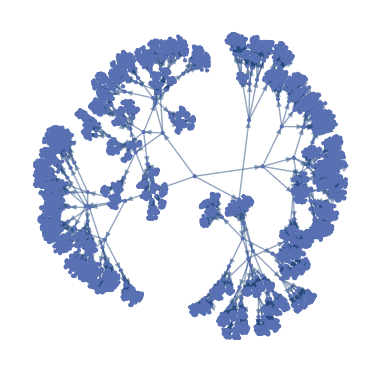

Number of Vertex=5461

```mathematica
(* Plot IBP Tree (it can be very slow!!!) *)
numberOfAtoms=9;
numberOfSlices=2; (* or 2 at max *)
node=3;
edges={};
count=3;
For[i=1,i≤2*numberOfSlices,i++,
AppendTo[edges,node->(++count)]
];
T=TreeGraph[edges];
For[k=5,k≤numberOfAtoms,k++,
leafs=Select[VertexList[T],VertexDegree[T,#]===1&];
count=Max[VertexList[T]];
For[i=1,i≤Length[leafs],i++,
node=leafs[[i]];
For[j=1,j≤2*numberOfSlices,j++,
AppendTo[edges,node->(++count)]
]
];
T=TreeGraph[edges];
]
Print[T]
Print["Number of Vertex=",Length[VertexList[T]]]
```

```mathematica
(* Number of nodes on IBP tree *)
NumberOfIBPVertex[numberOfAtoms_,numberOfSlices_]:=Module[{},((2*numberOfSlices)^(numberOfAtoms-2)-1)/((2*numberOfSlices)-1)];
NumberOfIBPVertex[9,1]
```

```mathematica
xy=Table[{i,NumberOfIBPVertex[9,i]},{i,10}];
ListLogPlot[xy,Joined->True,PlotLabel->"Number of Vertex on IBP Tree"]
```

```mathematica
(* Top 1: Sunway TaihuLight at 93 petaflops (10^15 flops) on November 2016 *)
xy=Table[{i,NumberOfIBPVertex[i,4]/(365*24*3600*(93*10^15))},{i,40}];
ListLogPlot[xy,Joined->True,PlotLabel->"Time to compute IBP tree on 93 petaflops",AxesLabel->{"Number of Atoms","Years"}]
```

## GASolver

### Source Code

#### GASolver

```mathematica
ClearAll[GASolver]
GANextBasis[G_,F_,U_,verbose_:False]:=Module[
{i,u,P,basis},
For[i=1,i≤Length[U],i++,
u=U[[i]];
P=Intersection[AdjacencyList[G,u],F];
If[Length[P]≥4,
basis=Take[P,4];
Return[basis]];
];
Throw["BasisCouldNotBeFound"];
];

GASetPosition[G_,X_,S_,basis_]:=Module[
{i,d,r,w,A,B,C,D,x,y,z,s,u,Y},
Y=Table[{0,0,0},{i,Length[S]}];
(* get basis coords *)
{x,y,z,s}=Table[X[[basis[[j]]]],{j,4}];
For[i=1,i≤Length[S],i++,
u=S[[i]];
(* get distances *)
r=Table[GetEdgeWeight[G,u->basis[[j]]],{j,4}];
(* get factors *) 
w={Sum[x[[j]]^2,{j,3}]-r[[1]]^2,Sum[y[[j]]^2,{j,3}]-r[[2]]^2,Sum[z[[j]]^2,{j,3}]-r[[3]]^2,Sum[s[[j]]^2,{j,3}]-r[[4]]^2};
A=0.5*{(x[[2]]*y[[3]]-x[[3]]*y[[2]])*w[[3]]+(x[[3]]*z[[2]]-x[[2]]*z[[3]])*w[[2]]+(y[[2]]*z[[3]]-y[[3]]*z[[2]])*w[[1]],(x[[3]]*y[[1]]-x[[1]]*y[[3]])*w[[3]]+(x[[1]]*z[[3]]-x[[3]]*z[[1]])*w[[2]]+(y[[3]]*z[[1]]-y[[1]]*z[[3]])*w[[1]],(x[[1]]*y[[2]]-x[[2]]*y[[1]])*w[[3]]+(x[[2]]*z[[1]]-x[[1]]*z[[2]])*w[[2]]+(y[[1]]*z[[2]]-y[[2]]*z[[1]])*w[[1]]};
B={x[[2]]*y[[3]]-x[[2]]*z[[3]]-x[[3]]*y[[2]]+x[[3]]*z[[2]]+y[[2]]*z[[3]]-y[[3]]*z[[2]],x[[3]]*y[[1]]-x[[3]]*z[[1]]-x[[1]]*y[[3]]+x[[1]]*z[[3]]+y[[3]]*z[[1]]-y[[1]]*z[[3]],x[[1]]*y[[2]]-x[[1]]*z[[2]]-x[[2]]*y[[1]]+x[[2]]*z[[1]]+y[[1]]*z[[2]]-y[[2]]*z[[1]]};
C=0.5*{(x[[1]]-z[[1]])*w[[2]]-(x[[1]]-y[[1]])*w[[3]]-(y[[1]]-z[[1]])*w[[1]],(x[[2]]-z[[2]])*w[[2]]-(x[[2]]-y[[2]])*w[[3]]-(y[[2]]-z[[2]])*w[[1]],(x[[3]]-z[[3]])*w[[2]]-(x[[3]]-y[[3]])*w[[3]]-(y[[3]]-z[[3]])*w[[1]]};
d=x[[1]]*y[[2]]*z[[3]]-x[[1]]*y[[3]]*z[[2]]-x[[2]]*y[[1]]*z[[3]]+x[[2]]*y[[3]]*z[[1]]+x[[3]]*y[[1]]*z[[2]]-x[[3]]*y[[2]]*z[[1]];
D={C[[2]]*s[[3]]-C[[3]]*s[[2]]-0.5*B[[1]]*w[[4]]+A[[1]],C[[3]]*s[[1]]-C[[1]]*s[[3]]-0.5*B[[2]]*w[[4]]+A[[2]],C[[1]]*s[[2]]-C[[2]]*s[[1]]-0.5*B[[3]]*w[[4]]+A[[3]],-Dot[A,s]+0.5*d*w[[4]],-Dot[B,s]+d};
Y[[i]]={D[[1]],D[[2]],D[[3]]}/D[[5]]
];
Return[Y]
];

GASolver[G_,verbose_:False]:=Module[
{i,d,x,y,z,r,s,u,w,basis,A,B,C,D,F,S,X,U},
{X,F}=BuildUpInitX[G,verbose];
U=Complement[Table[i,{i,Length[VertexList[G]]}],F];
(*set the remaining atoms*)
While[Length[U]>0,
basis=GANextBasis[G,F,U,verbose];
(* find atoms to set position *)
S=Intersection[AdjacencyList[G,basis[[1]]],U];
S=Intersection[AdjacencyList[G,basis[[2]]],S];
S=Intersection[AdjacencyList[G,basis[[3]]],S];
S=Intersection[AdjacencyList[G,basis[[4]]],S];
If[verbose,Print["F=",F," U=",U," basis=",basis," S=",S]];
X[[S]]=GASetPosition[G,X,S,basis];
F=Union[F,S];
U=Complement[U,S]
];
Return[X]
];
```

#### GASolver2 (Not working)

```mathematica
(*GASolver2[G_]:=Module[
{i,j,d,x,y,z,s,numberOfAtoms,A,C,B,D,Y,M,X,S,U2,U3,U4,V3,V4},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{i,numberOfAtoms}];
(* set the position of the first four atoms *)
X[[2]][[1]]=GetEdgeWeight[G,1->2];U2=X[[2]][[1]];
X[[3]][[1]]=(GetEdgeWeight[G,3->1]^2-GetEdgeWeight[G,3->2]^2+U2^2)/(2*U2);U3=X[[3]][[1]];
X[[3]][[2]]=Sqrt[GetEdgeWeight[G,3->1]^2-U3^2];V3=X[[3]][[2]];
X[[4]][[1]]=(GetEdgeWeight[G,4->1]^2-GetEdgeWeight[G,4->2]^2+U2^2)/(2*U2);U4=X[[4]][[1]];
X[[4]][[2]]=(GetEdgeWeight[G,4->2]^2-GetEdgeWeight[G,4->3]^2-(U4-U2)^2+(U4-U3)^2+V3^2)/(2*V3);V4=X[[4]][[2]];
X[[4]][[3]]=Sqrt[GetEdgeWeight[G,4->1]^2-U4^2-V4^2];
(* set the remaining atoms *)
For[i=5,i≤numberOfAtoms,i++,
P=Select[AdjacencyList[G,i],#<i&];
If[Length[P]<4,Throw["NotEnoughAdjacentNodes"]];
Y=Table[X[[P[[j]]]],{j,4}];
S=Y[[4]];
(* squared distances *)
z=Table[Norm[Y[[j]]]^2-GetEdgeWeight[G,i->P[[j]]]^2,{j,4}];
M=Transpose[{Cross[Y[[2]],Y[[3]]],Cross[Y[[3]],Y[[1]]],Cross[Y[[2]],Y[[1]]]}];
A=0.5*(M.z[[1;;3]]);
B=Table[Sum[M[[k,j]],{j,3}],{k,3}];
C=0.5*(Transpose[{Y[[3]]-Y[[2]],Y[[1]]-Y[[3]],Y[[2]]-Y[[1]]}].z[[1;;3]]);
d =Det[Y[[1;;3]]];Print["Det(A)=",d];
D={C[[2]]*S[[3]]-C[[3]]*S[[2]]-B[[1]]*z[[4]]/2+A[[1]],
C[[3]]*S[[1]]-C[[1]]*S[[3]]-B[[2]]*z[[4]]/2+A[[2]],
C[[1]]*S[[2]]-C[[2]]*S[[1]]-B[[3]]*z[[4]]/2+A[[3]],
-Dot[A,S]+d*z[[4]]/2,
-Dot[B,S]+d};
X[[i]]={D[[1]],D[[2]],D[[3]]}/D[[5]];
];
Return[X]
];*)
```

### Example

```mathematica
M=GenerateRandomMDG[150,5,"DistanceMatrix",0];
X=M["X"];
G=M["G"];
S=GASolver[G,False];
Print["LDME=",LDME[G,S]]
```

## Comparisons

### Speed

```mathematica
M=GenerateRandomMDG[350,5,"DistanceMatrix",0];
G=M["G"];
Print["GA      = ",Timing[S=GASolver[G,False];]]
Print["BuildUp = ",Timing[Y=BuildUpSolver[G,False];]]
Print["LDME(GA)      = ",LDME[G,S]]
Print["LDME(BuildUp) = ",LDME[G,Y]]
```

### Robustness

#### Example: Colinear Points

```mathematica
(*z=Table[10^(i),{i,1,16}];
a=Table[0,{i,Length[z]}];
b=Table[0,{i,Length[z]}];
For[k=1,k≤Length[z],k++,
X={{0,0,0},{1,0,0},{0.5,1/z[[k]],0},{1,2,3}};
(* build graph *)
edges={};
weights={};
For[i=1,i≤4,i++,
For[j=i+1,j≤4,j++,
AppendTo[edges,i<->j];
AppendTo[weights,Norm[X[[i]]-X[[j]]]]
];
];
G=Graph[edges,EdgeWeight->weights];
Z=BPGetNodePosition[G,X,4,{1,1,1,1}];
Print["k= ",k,"  Log10[E]= ", Log10[Norm[X[[4]]-Z]] ]
];*)
```

#### Example B

```mathematica
z=Table[10^(-i),{i,0,12}];
a=Table[0,{i,Length[z]}];
b=Table[0,{i,Length[z]}];
For[k=1,k≤Length[z],k++,
X={{0,0,0},{1,0,0},{0,1,0},{1,1,z[[k]]},{.5,.5,1}};
(* build graph *)
edges={};
weights={};
For[i=1,i≤5,i++,
For[j=i+1,j≤5,j++,
AppendTo[edges,i<->j];
AppendTo[weights,Norm[X[[i]]-X[[j]]]]
];
];
G=Graph[edges,EdgeWeight->weights];
S={5};
basis={1,2,3,4};
a[[k]]=Norm[X[[S]]-BuildUpSetPosition[G,X,S,basis]];
b[[k]]=Norm[X[[S]]-GASetPosition[G,X,S,basis]]
];
```

## Articles:

### MMAS' 17

#### Problem

```mathematica
vertices={1,2,3,4,5,6};
(* create edges *)
edges={};
For[j=1,j≤3,j++,
For[k=1,k≤(Length[vertices]-j),k++,AppendTo[edges,k<->(k+j)]]
];
(* extra distances *)
AppendTo[edges,1<->5];
(* create graph *)
G=Graph[vertices,edges];
(* set edges values *)
For[k=1,k≤(Length[vertices]-1),k++,
PropertyValue[{G,k<->(k+1)},EdgeWeight]=1;
PropertyValue[{G,k<->(k+1)},"DistanceBounds"]={1,1}
]
For[k=1,k≤(Length[vertices]-2),k++,
PropertyValue[{G,k<->(k+2)},EdgeWeight]=Sqrt[3];
PropertyValue[{G,k<->(k+2)},"DistanceBounds"]={Sqrt[3],Sqrt[3]}
]
PropertyValue[{G,1<->4},EdgeWeight]=2.15;
PropertyValue[{G,1<->4},"DistanceBounds"]={2.15,2.15};
PropertyValue[{G,1<->5},EdgeWeight]=0;
PropertyValue[{G,1<->5},"DistanceBounds"]={2.45,2.55};
PropertyValue[{G,2<->5},EdgeWeight]=0;
PropertyValue[{G,2<->5},"DistanceBounds"]={2.2,2.6};
PropertyValue[{G,3<->6},EdgeWeight]=0;
PropertyValue[{G,3<->6},"DistanceBounds"]={2.4,2.6};
Print["G=",G]
Print["EdgesList[G]=",EdgeList[G]]
```

#### Getting Reference Solution

```mathematica
ClearAll[DGApplyRotors]
DGApplyRotors[X_,ω_]:=Module[{i,j,Y},
Y=Table[X[[i]],{i,Length[X]}];
For[i=4,i≤Length[X],i++,
For[j=i,j≤Length[X],j++,
Y[[j]]=RotationTransform[ω[[i]],Y[[i-1]]-Y[[i-2]],Y[[i-1]]][Y[[j]]]
];
];
Return[Y]
];

(* Create BP instance by removing the edge 1<->5 and choosing the lower bounds *)
H=EdgeDelete[G,1<->5];
PropertyValue[{H,2<->5},EdgeWeight]=PropertyValue[{H,2<->5},"DistanceBounds"][[1]];
PropertyValue[{H,3<->6},EdgeWeight]=PropertyValue[{H,3<->6},"DistanceBounds"][[1]];
Print["H=",H]
Print["EdgesList[H]=",EdgeList[H]]
(* solving *)
{S,work}=BPSolver[H];
XL=S["Points"];
BL=S["Branches"];
```

```mathematica
(* Create BP instance from H and choosing the upper bounds *)
PropertyValue[{H,2<->5},EdgeWeight]=PropertyValue[{H,2<->5},"DistanceBounds"][[2]];
PropertyValue[{H,3<->6},EdgeWeight]=PropertyValue[{H,3<->6},"DistanceBounds"][[2]];
(* solving *)
{S,work}=BPSolver[H];
XU=S["Points"];
BU=S["Branches"];
```

```mathematica
For[i=1,i≤Length[XL],i++,
Print[{i,XL[[i]][[5]],BL[[i]]}]
]
```

```mathematica
For[i=1,i≤Length[XU],i++,
Print[{i,XU[[i]][[5]],BU[[i]]}]
]
```

```mathematica
ω0=DGCalculateTorsionAngles[XL[[3]]]
```

```mathematica
DGCalculateTorsionAngles[{{{0,0,0},{-1.526,0,0},{-2.0337555109089696,1.4390484151485563,0},{-3.547672337964905,1.443311855896645,-0.19160809959361638},{-4.055116583577064,2.8824679631395647,-0.1940650449558058},{-5.535245944780861,2.898338552188936,-0.5650653124835617},{-6.314751736361553,2.0310259548177694,0.41921898553883463},{-5.8519784317208705,0.5821023754385368,0.2961851299103264},{-4.351017496990884,0.5043057015628287,0.560268355330575}},{{0,0,0},{-1.526,0,0},{-2.0337555109089696,1.4390484151485563,0},{-3.547672337964905,1.443311855896645,0.19160809959361638},{-4.055116583577064,2.8824679631395647,0.1940650449558058},{-5.535245944780861,2.898338552188936,0.5650653124835617},{-6.314751736361553,2.0310259548177694,-0.41921898553883463},{-5.8519784317208705,0.5821023754385368,-0.2961851299103264},{-4.351017496990884,0.5043057015628287,-0.560268355330575}}}⟦3⟧]
```

```mathematica
ω1=DGCalculateTorsionAngles[XU[[3]]]
```

```mathematica
X=XL[[1]];
Y=DGApplyRotors[X,{0,0,0,0,0.56,0}]
MatrixForm[DistanceMatrix[X]]
MatrixForm[DistanceMatrix[Y]]
ω5={0.56,0.62,0.733};
Y=Table[DGApplyRotors[X,{0,0,0,0,ω5[[i]],0}],{i,Length[ω5]}];
Z=DGApplyRotors[X,{0,0,0,0,0.68,0}];
figs=Table[{Line[Y[[i]]],{PointSize[.025],LightGray,Point[Y[[i]]]}},{i,Length[Y]}];
figs=Prepend[figs,{Line[Z],{PointSize[.025],Black,Point[Z]}}];
Graphics3D[figs, Axes->False]
```

```mathematica
DGApplyRotors[XL⟦1⟧,{0,0,0,0,0.56,0}]
```

```mathematica
DistanceMatrix[DGApplyRotors[XL⟦1⟧,{0,0,0,0,0.56,0}]]
```

```mathematica
ω6={0.56,0.62,0.68,0.733};
Y=Table[ApplyRotors[X,{0,0,0,0,0.68,ω6[[i]]}],{i,Length[ω6]}];
figs=Prepend[figs,Table[{Line[Y[[i]]],{PointSize[.025],LightGray,Point[Y[[i]]]}},{i,Length[Y]}]];
Graphics3D[figs, Axes->False]
```

-Graphics3D-